```mathematica
Drop mode (n = 200)
```

General::munfl: (1.37818×10^-7)^200 is too small to represent as a normalized machine number; precision may be lost.

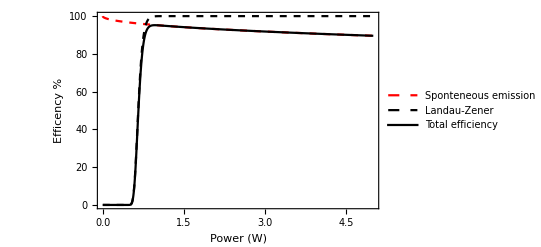

9-22-22-16.png

```mathematica
ClearAll[No,A,r,Vo,n,θ,theta,P,Δ]
nm =10^(-9);MHz=10^6;GHz=10^9;mm=10^(-3);ms=10^(-3);
A[r_]=4*Pi*r*r; (*Area*)
Subscript[I, sat]=30.5;(*Saturation intensity (SI unit)*)
λ=780nm; (*wavelength*)
k=2*Pi/λ;(*wavevector*)
Γ=2*Pi*6.065MHz;
ℏ =1.054571 *10^(-34);
m= 1.4431*10^(-25);
Er = 4*ℏ*ℏ*k*k*0.5/m;
ωr = Er/ℏ;

theta=0;(*Imperfect standing wave with θ angle*)
detuning=300GHz; (*Laser detuning*)
radius=5mm;(*Beam waist (radius)*)
n=200; (*#momentum kick*)
acctime=10 ms; (*acceleration/deceleration time*)

Subscript[R, sc][P_,Δ_,r_]=(Γ*0.5*(P/(A[r]*Subscript[I, sat])))/((2Δ/Γ)^2); (*Scattering rate due to spontaneous emissio*)
Subscript[η, lat][P_,Δ_,r_]=(2*2*Pi/(Γ*λ))((ℏ*Δ/m)^0.5)((Subscript[I, sat]*A[r]/P)^0.5);(*Suppression factor*)
Subscript[η, tot][P_,Δ_,r_,θ_]= 4((Sin[0.5*θ])^2) + Subscript[η, lat][P,Δ,r]((((Cos[0.5*θ])^2)-((Sin[0.5*θ])^2))^0.5);(*Imperfect standing wave with θ angle*)
Subscript[F, sp][P_,Δ_,r_,θ_,τ_]= Exp[-Subscript[η, tot][P,Δ,r,θ]*Subscript[R, sc][P,Δ,r]*τ];(*Fraction surviving the launch despite of spontaneous emission loss*)

Vo[P_,Δ_,r_]= ℏ*Γ*0.5*((P/(A[r]))/Subscript[I, sat])/((Δ/Γ)*Er);
Subscript[Ω, eff][P_,Δ_,r_]= Vo[P,Δ,r]*ωr*0.5;
α[No_,τ_]=No*ωr/τ;
Subscript[F, LZ][No_,P_,Δ_,τ_,r_]=(1-Exp[-0.5*Pi*((Subscript[Ω, eff][P,Δ,r])^2)/α[No,τ]])^No;
Frac[P_]=1;
Ftot[P_,Δ_,r_,θ_,τ_,No_,r_]=(Subscript[F, sp][P,Δ,r,θ,τ])*(Subscript[F, LZ][No,P,Δ,τ,r]);

Finalpower=5;

p1=Plot[100*(Subscript[F, sp][P,detuning,radius,theta,acctime]),{P,0,Finalpower},PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Sponteneous emission"},PlotStyle->{Red,Dashed}];
p2=Plot[100*(Subscript[F, LZ][n,P,detuning,acctime,radius]),{P,0,Finalpower},PlotRange->All,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Landau-Zener"},PlotStyle->{Black,Dashed}];
p3=Plot[100*(Ftot[P,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Total efficiency"},PlotStyle->{Black,Thick}];
Show[p1,p2,p3]
Export["9-22-22-16.png",Show[p1,p2,p3]]
```

```mathematica
Launch mode (n = 200)
```

General::munfl: (2.29697×10^-8)^1200 is too small to represent as a normalized machine number; precision may be lost.

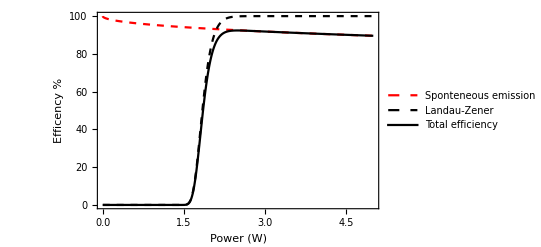

9-22-22-16.png

```mathematica
ClearAll[No,A,r,Vo,n,θ,theta,P,Δ,τ]
nm =10^(-9);MHz=10^6;GHz=10^9;mm=10^(-3);ms=10^(-3);
A[r_]=4*Pi*r*r; (*Area*)
Subscript[I, sat]=30.5;(*Saturation intensity (SI unit)*)
λ=780nm; (*wavelength*)
k=2*Pi/λ;(*wavevector*)
Γ=2*Pi*6.065MHz;
ℏ =1.054571 *10^(-34);
m= 1.4431*10^(-25);
Er = 4*ℏ*ℏ*k*k*0.5/m;
ωr = Er/ℏ;

theta=0;(*Imperfect standing wave with θ angle*)
detuning=300GHz; (*Laser detuning*)
radius=5mm;(*Beam waist (radius)*)
n=1200; (*#momentum kick*)
acctime=10 ms; (*acceleration/deceleration time*)

Subscript[R, sc][P_,Δ_,r_]=(Γ*0.5*(P/(A[r]*Subscript[I, sat])))/((2Δ/Γ)^2); (*Scattering rate due to spontaneous emissio*)
Subscript[η, lat][P_,Δ_,r_]=(2*2*Pi/(Γ*λ))((ℏ*Δ/m)^0.5)((Subscript[I, sat]*A[r]/P)^0.5);(*Suppression factor*)
Subscript[η, tot][P_,Δ_,r_,θ_]= 4((Sin[0.5*θ])^2) + Subscript[η, lat][P,Δ,r]((((Cos[0.5*θ])^2)-((Sin[0.5*θ])^2))^0.5);(*Imperfect standing wave with θ angle*)
Subscript[F, sp][P_,Δ_,r_,θ_,τ_]= Exp[-Subscript[η, tot][P,Δ,r,θ]*Subscript[R, sc][P,Δ,r]*τ];(*Fraction surviving the launch despite of spontaneous emission loss*)

Vo[P_,Δ_,r_]= ℏ*Γ*0.5*((P/(A[r]))/Subscript[I, sat])/((Δ/Γ)*Er);
Subscript[Ω, eff][P_,Δ_,r_]= Vo[P,Δ,r]*ωr*0.5;
α[No_,τ_]=No*ωr/τ;
Subscript[F, LZ][No_,P_,Δ_,τ_,r_]=(1-Exp[-0.5*Pi*((Subscript[Ω, eff][P,Δ,r])^2)/α[No,τ]])^No;
Frac[P_]=1;
Ftot[P_,Δ_,r_,θ_,τ_,No_,r_]=(Subscript[F, sp][P,Δ,r,θ,τ])*(Subscript[F, LZ][No,P,Δ,τ,r]);

Finalpower=5;

p1=Plot[100*(Subscript[F, sp][P,detuning,radius,theta,acctime]),{P,0,Finalpower},PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Sponteneous emission"},PlotStyle->{Red,Dashed}];
p2=Plot[100*(Subscript[F, LZ][n,P,detuning,acctime,radius]),{P,0,Finalpower},PlotRange->All,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Landau-Zener"},PlotStyle->{Black,Dashed}];
p3=Plot[100*(Ftot[P,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Total efficiency"},PlotStyle->{Black,Thick}];
Show[p1,p2,p3]
Export["9-22-22-16.png",Show[p1,p2,p3]]
```

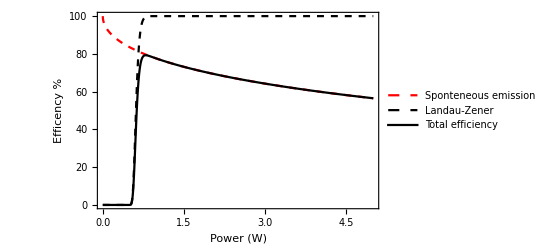

9-22-22-16.png

```mathematica
MHz=10^6;GHz=10^9;mm=10^(-3); mW =10^(-3);

Γ=2*Pi*6.06MHz; (*Natural linewidth*)
Isat=25.5; (*Saturation intencity in SI units- linearly polarized light*)
Δ = 8.86GHz;  (*Detuning of laser*)

r=5.5mm;   (*Beam waist*)
P1=10 mW;  (*Power*)
P2=10 mW;
I1 = P1/(4*Pi*r*r); (*Intensity*)
I2 = P2/(4*Pi*r*r);
Subscript[Ω, eff][I1_,I2_,Δ_]=Γ(((I1/Isat)*(I2/Isat))^0.5)/(4*(Δ/Γ)) (*Rabi frequency*)

Subscript[τ, half][I1_,I2_,Δ_]=(10^6)Pi*0.5/Subscript[Ω, eff][I1,I2,Δ] (*pi/2 pulse timing in μs*)
Subscript[τ, pi][I1_,I2_,Δ_]=(10^6)Pi/Subscript[Ω, eff][I1,I2,Δ](*pi pulse timing in μs*)
```

42202.3

37.2207

74.4413

```mathematica
Subscript[τ, half][I1,I2,-8.86 GHz]
```

0.50247